```mathematica
n = 7;
T = 10;
X = {{0.5422367394933054,0.6904641104103801,0.6407769116356902,0.6878171268293168,0.4739922469537595,0.740787055864177,0.5510330650007719},{0.6926895081996918,0.685990571812324,0.6010490883474688,0.6239970200911067,0.4972732697121849,0.669838766210283,0.5570943786620931},{0.7194078330470648,0.6263558104699439,0.6171841228626438,0.529494590116441,0.5130255264229324,0.6666157192888184,0.5379764346657545},{0.6563964440818612,0.5935132442777122,0.5933324073326132,0.6216137176309025,0.5066116190791847,0.7424314670214157,0.4901703939901842},{0.6628460325390879,0.8096088266372681,0.6439330169479647,0.649233095255323,
0.5460082866724272,0.5716514442897859,0.6327343093454403},{0.7270600312880214,0.6652893293010491,0.6483830346930366,0.7081364666288095,0.5941668300891308,0.7371603026961917,0.7661281174050248},{0.5824143675994357,0.5296536682327806,0.601565806467557,0.5982206207923645,0.5239878860811674,0.655859087952008,0.5745106966401501},{0.5771693677845203,0.6788740313613554,0.5685347894433006,0.6045270016322508,0.5452230344330624,0.6366051686697941,0.6533988873101869},{0.6589907092930617,0.6594582686218584,0.6100529832408768,0.6071422663335075,0.5719417412401707,0.6696638025996607,0.6944493598683641},{0.8083277594245356,0.6825808760786612,0.552651113948973,0.6008581478693906,0.5738377038384218,0.710904152986947,0.6795840097687782}};
```

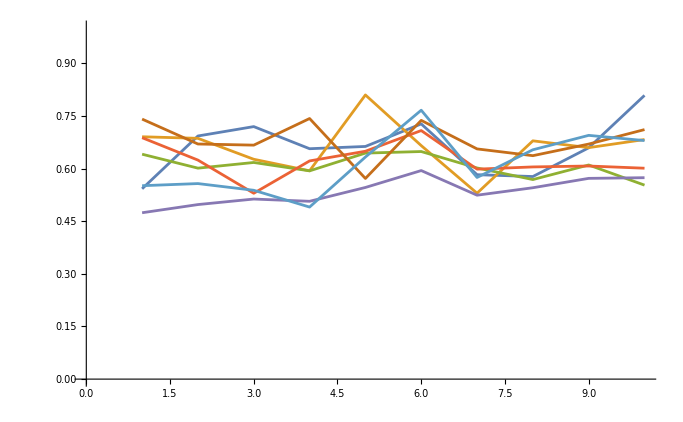

```mathematica
ListLinePlot[Transpose[X],PlotRange -> {0, 1}]
```

```mathematica
W = Table[Subscript[w, i, j] , {i, 1, n}, {j, 1, n}];
S = Table[Subscript[s, i], {i, 1, n}];
A = Table[Subscript[a, i, j], {i, 1, n}, {j, 1, n}];
Φ = Table[Subscript[ϕ, i], {i, 1, n}];
Xt1=Table[Subscript[xt1, i], {i, 1, n}];
Xt=Table[Subscript[xt, i], {i, 1, n}];
Z=Table[Subscript[z, i], {i, 1, n}];
```

```mathematica
solveFJ = NMinimize[
   {
    Sum[(X[[t + 1]] - DiagonalMatrix[S] . W . X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).Z) . (X[[t + 1]] - DiagonalMatrix[S] . W . X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).Z), {t, 1,T - 1}],
    Flatten[W] ≥ ConstantArray[0, n^2],
    Flatten[W] ≤ ConstantArray[1, n^2],
    Flatten[S]≤ ConstantArray[1, n],
    Flatten[S]≥ ConstantArray[0, n],
Flatten[Z]≤ ConstantArray[1, n],
    Flatten[Z]≥ ConstantArray[0, n],
    Total[Transpose[W]] == ConstantArray[1, n]
    } ,Flatten[{W,S,Z}],MaxIterations -> 800,AccuracyGoal ->6];
```

```mathematica
solveFJ
```

{0.164657,{w_(1,1)→9.91884×10^-9,w_(1,2)→1.,w_(1,3)→0.,w_(1,4)→0.,w_(1,5)→0.,w_(1,6)→0.,w_(1,7)→0.,w_(2,1)→3.5508×10^-8,w_(2,2)→4.20255×10^-8,w_(2,3)→4.15226×10^-7,w_(2,4)→1.7185×10^-7,w_(2,5)→9.95912×10^-9,w_(2,6)→4.446×10^-8,w_(2,7)→0.999999,w_(3,1)→0.104515,w_(3,2)→0.662543,w_(3,3)→0.,w_(3,4)→0.,w_(3,5)→0.,w_(3,6)→0.232942,w_(3,7)→0.,w_(4,1)→-3.37414×10^-8,w_(4,2)→0.291923,w_(4,3)→0.693512,w_(4,4)→0.,w_(4,5)→0.0145651,w_(4,6)→0.,w_(4,7)→0.,w_(5,1)→-4.60123×10^-8,w_(5,2)→0.199942,w_(5,3)→0.,w_(5,4)→0.,w_(5,5)→0.800058,w_(5,6)→0.,w_(5,7)→0.,w_(6,1)→0.172896,w_(6,2)→0.493855,w_(6,3)→0.260714,w_(6,4)→0.,w_(6,5)→0.,w_(6,6)→0.,w_(6,7)→0.0725346,w_(7,1)→-1.17062×10^-7,w_(7,2)→0.330948,w_(7,3)→0.,w_(7,4)→0.,w_(7,5)→0.669052,w_(7,6)→0.,w_(7,7)→0.,s_1→0.486108,s_2→0.,s_3→0.334722,s_4→0.567576,s_5→0.550916,s_6→0.675789,s_7→0.890439,z_1→0.6915,z_2→0.659035,z_3→0.574713,z_4→0.602555,z_5→0.523147,z_6→0.739478,z_7→1.}}

```mathematica
D[(txt1-txt.tw).(xtq-w.xt),{w,1}]
D[(txt1-txt.tw.ts-tx0.(1-ts)).(xt1-s.w.xt-(1-s).x0),{w,s}]
```

(txt1-txt.tw).(-1.xt)

∂_{w,s} ((txt1-tx0.(1-ts)-txt.tw.ts).(xt1-(1-s).x0-s.w.xt))

# DeGroot

check rules for DeGroot by first method

```mathematica
m=Min/@X
M=Max/@X
```

{0.473992,0.497273,0.513026,0.49017,0.546008,0.594167,0.523988,0.545223,0.571942,0.552651}

{0.740787,0.69269,0.719408,0.742431,0.809609,0.766128,0.655859,0.678874,0.694449,0.808328}

```mathematica
μ=Table[(X[[t]]-m[[t-1]])/(M[[t-1]]-m[[t-1]]),{t,2,T}]
```

{{0.819721,0.794612,0.476234,0.562248,0.0872619,0.734072,0.311483},{1.13673,0.660552,0.613618,0.164886,0.0806087,0.866573,0.20829},{0.694686,0.389993,0.389117,0.526151,-0.0310778,1.11156,-0.110742},{0.684512,1.2663,0.609538,0.630548,0.22135,0.323003,0.565144},{0.686841,0.452507,0.388371,0.615053,0.182695,0.725158,0.835051},{-0.0683437,-0.375161,0.043027,0.0235739,-0.408109,0.358757,-0.114306},{0.403284,1.17453,0.337806,0.610741,0.161029,0.853995,0.981344},{0.85123,0.854728,0.485069,0.46329,0.199914,0.931087,1.11654},{1.92956,0.90312,-0.157465,0.236038,0.0154763,1.13432,0.878658}}

```mathematica
μ//MatrixForm
```

(0.819721 | 0.794612 | 0.476234 | 0.562248 | 0.0872619 | 0.734072 | 0.311483
1.13673 | 0.660552 | 0.613618 | 0.164886 | 0.0806087 | 0.866573 | 0.20829
0.694686 | 0.389993 | 0.389117 | 0.526151 | -0.0310778 | 1.11156 | -0.110742
0.684512 | 1.2663 | 0.609538 | 0.630548 | 0.22135 | 0.323003 | 0.565144
0.686841 | 0.452507 | 0.388371 | 0.615053 | 0.182695 | 0.725158 | 0.835051
-0.0683437 | -0.375161 | 0.043027 | 0.0235739 | -0.408109 | 0.358757 | -0.114306
0.403284 | 1.17453 | 0.337806 | 0.610741 | 0.161029 | 0.853995 | 0.981344
0.85123 | 0.854728 | 0.485069 | 0.46329 | 0.199914 | 0.931087 | 1.11654
1.92956 | 0.90312 | -0.157465 | 0.236038 | 0.0154763 | 1.13432 | 0.878658)

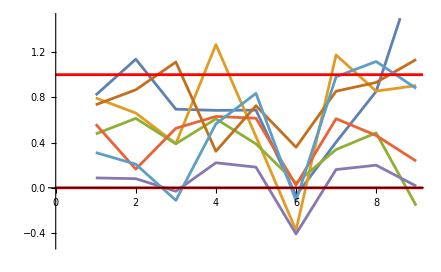

```mathematica
p1=ListLinePlot[Transpose[μ],PlotRange -> {-0.5,1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

check rules for DeGroot by second method

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.684513 | 1.2663 | 0.609539 | 0.63055 | 0.221351 | 0.323005 | 0.565146
0.741581 | 0.548209 | 0.495284 | 0.682341 | 0.325561 | 0.7732 | 0.863884
0.28877 | 0.123603 | 0.348723 | 0.338251 | 0.105866 | 0.518688 | 0.264028
0.186196 | 0.542278 | 0.155965 | 0.281979 | 0.0743469 | 0.394289 | 0.453086
0.55754 | 0.559471 | 0.355435 | 0.343414 | 0.198041 | 0.601618 | 0.703979
1.66806 | 0.930376 | 0.168151 | 0.450954 | 0.292441 | 1.09653 | 0.912795)

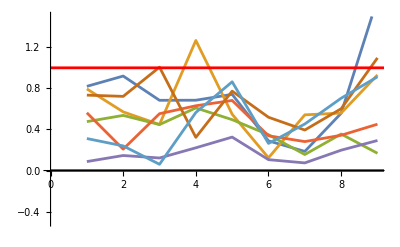

```mathematica
step=2;
mt={0.473992,0.473992,0.473992,0.49017,0.49017,0.49017,0.523988,0.523988,0.523988,0.545223};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.766128,0.694449,0.808328};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.741581 | 0.548209 | 0.495284 | 0.682341 | 0.325561 | 0.7732 | 0.863884
0.28877 | 0.123603 | 0.348723 | 0.338251 | 0.105866 | 0.518688 | 0.264028
0.27235 | 0.590736 | 0.24532 | 0.357993 | 0.172343 | 0.458414 | 0.510986
0.472664 | 0.474301 | 0.301326 | 0.291135 | 0.167893 | 0.510032 | 0.59681
1.17428 | 0.654964 | 0.118374 | 0.317462 | 0.205871 | 0.771934 | 0.642587)

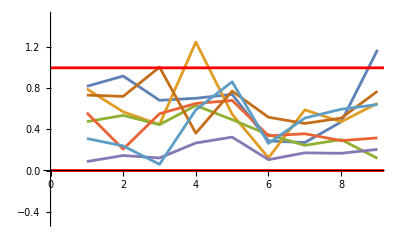

```mathematica
step=3;
mt={0.473992,0.473992,0.473992,0.473992,0.49017,0.49017,0.49017,0.523988,0.523988,0.523988};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.766128,0.808328};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.754038 | 0.569987 | 0.519613 | 0.697654 | 0.358071 | 0.784133 | 0.870445
0.28877 | 0.123603 | 0.348723 | 0.338251 | 0.105866 | 0.518688 | 0.264028
0.27235 | 0.590736 | 0.24532 | 0.357993 | 0.172343 | 0.458414 | 0.510986
0.528491 | 0.529955 | 0.375292 | 0.36618 | 0.255985 | 0.561903 | 0.639494
0.995514 | 0.555256 | 0.100354 | 0.269133 | 0.174531 | 0.65442 | 0.544764)

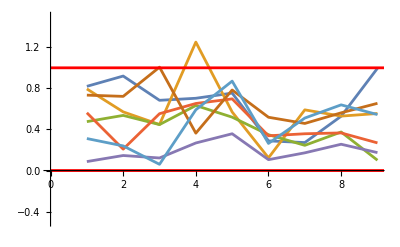

```mathematica
step=4;
mt={0.473992,0.473992,0.473992,0.473992,0.473992,0.49017,0.49017,0.49017,0.523988,0.523988};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.809609,0.808328};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.754038 | 0.569987 | 0.519613 | 0.697654 | 0.358071 | 0.784133 | 0.870445
0.323054 | 0.165849 | 0.380117 | 0.37015 | 0.148967 | 0.541889 | 0.299504
0.27235 | 0.590736 | 0.24532 | 0.357993 | 0.172343 | 0.458414 | 0.510986
0.528491 | 0.529955 | 0.375292 | 0.36618 | 0.255985 | 0.561903 | 0.639494
0.995989 | 0.60234 | 0.195596 | 0.346508 | 0.261921 | 0.691006 | 0.592958)

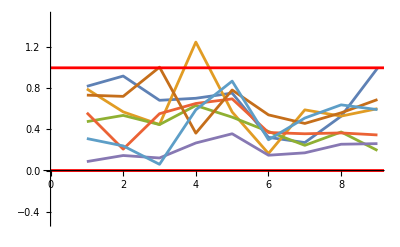

```mathematica
step=5;
mt={0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.49017,0.49017,0.49017,0.523988};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.809609,0.809609};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.754038 | 0.569987 | 0.519613 | 0.697654 | 0.358071 | 0.784133 | 0.870445
0.323054 | 0.165849 | 0.380117 | 0.37015 | 0.148967 | 0.541889 | 0.299504
0.307426 | 0.610464 | 0.281698 | 0.38894 | 0.212239 | 0.48452 | 0.534558
0.528491 | 0.529955 | 0.375292 | 0.36618 | 0.255985 | 0.561903 | 0.639494
0.995989 | 0.60234 | 0.195596 | 0.346508 | 0.261921 | 0.691006 | 0.592958)

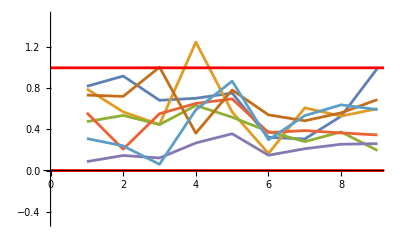

```mathematica
step=6;
mt={0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.49017,0.49017,0.49017};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.809609,0.809609};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.754038 | 0.569987 | 0.519613 | 0.697654 | 0.358071 | 0.784133 | 0.870445
0.323054 | 0.165849 | 0.380117 | 0.37015 | 0.148967 | 0.541889 | 0.299504
0.307426 | 0.610464 | 0.281698 | 0.38894 | 0.212239 | 0.48452 | 0.534558
0.55122 | 0.552613 | 0.405406 | 0.396733 | 0.29185 | 0.583021 | 0.656872
0.995989 | 0.60234 | 0.195596 | 0.346508 | 0.261921 | 0.691006 | 0.592958)

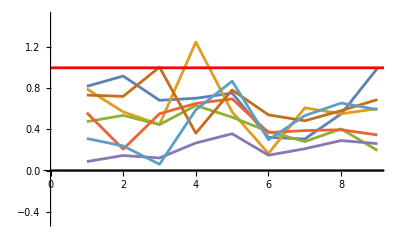

```mathematica
step=7;
mt={0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.49017,0.49017};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.809609,0.809609};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.754038 | 0.569987 | 0.519613 | 0.697654 | 0.358071 | 0.784133 | 0.870445
0.323054 | 0.165849 | 0.380117 | 0.37015 | 0.148967 | 0.541889 | 0.299504
0.307426 | 0.610464 | 0.281698 | 0.38894 | 0.212239 | 0.48452 | 0.534558
0.55122 | 0.552613 | 0.405406 | 0.396733 | 0.29185 | 0.583021 | 0.656872
0.996182 | 0.621509 | 0.234372 | 0.378009 | 0.297499 | 0.7059 | 0.612579)

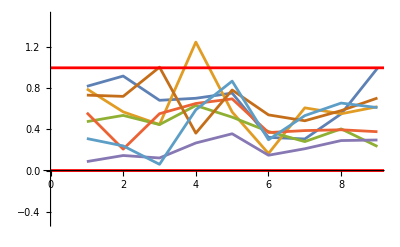

```mathematica
step=8;
mt={0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.49017};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.809609,0.809609};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

```mathematica
step=9;
mt={0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.809609,0.809609};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.754038 | 0.569987 | 0.519613 | 0.697654 | 0.358071 | 0.784133 | 0.870445
0.323054 | 0.165849 | 0.380117 | 0.37015 | 0.148967 | 0.541889 | 0.299504
0.307426 | 0.610464 | 0.281698 | 0.38894 | 0.212239 | 0.48452 | 0.534558
0.55122 | 0.552613 | 0.405406 | 0.396733 | 0.29185 | 0.583021 | 0.656872
0.996182 | 0.621509 | 0.234372 | 0.378009 | 0.297499 | 0.7059 | 0.612579)

-Graphics-

```mathematica
step=10;
mt={0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992,0.473992};
Mt={0.740787,0.740787,0.740787,0.742431,0.809609,0.809609,0.809609,0.809609,0.809609,0.809609};
μ2=Table[(X[[t]]-mt[[t-1]])/(Mt[[t-1]]-mt[[t-1]]),{t,2,T}];
μ2//MatrixForm
p1=ListLinePlot[Transpose[μ2],PlotRange -> {-0.5, 1.5}];
p2=ContourPlot[{y==1},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
p3=ContourPlot[{y==0},{x,0,10},{y,-5,5},Axes->True,Frame->False,ContourStyle->Red];
Show[p1,p2,p3]
```

(0.819721 | 0.794612 | 0.476235 | 0.562248 | 0.0872628 | 0.734072 | 0.311484
0.919867 | 0.571089 | 0.536712 | 0.208035 | 0.146305 | 0.721991 | 0.239826
0.683688 | 0.447989 | 0.447311 | 0.553315 | 0.122265 | 1.00616 | 0.0606398
0.703527 | 1.25025 | 0.633071 | 0.652815 | 0.268278 | 0.363805 | 0.591353
0.754038 | 0.569987 | 0.519613 | 0.697654 | 0.358071 | 0.784133 | 0.870445
0.323054 | 0.165849 | 0.380117 | 0.37015 | 0.148967 | 0.541889 | 0.299504
0.307426 | 0.610464 | 0.281698 | 0.38894 | 0.212239 | 0.48452 | 0.534558
0.55122 | 0.552613 | 0.405406 | 0.396733 | 0.29185 | 0.583021 | 0.656872
0.996182 | 0.621509 | 0.234372 | 0.378009 | 0.297499 | 0.7059 | 0.612579)

-Graphics-

```mathematica
FunctionConvexity[
Sum[(X[[t+1]]-W.X[[t]]).(X[[t+1]]-W.X[[t]]),{t,1,T-1}]
,Flatten[W]
]
```

1

```mathematica
solveDG = NMinimize[
   {
    Sum[(X[[t + 1]] - W . X[[t]]) . (X[[t + 1]] - W . X[[t]]), {t, 1, 
      T - 1}],
    Flatten[W] ≥ ConstantArray[0, n^2],
    Flatten[W] ≤ ConstantArray[1, n^2],
    Total[Transpose[W]] == ConstantArray[1, n]
    } ,
   Flatten[W],AccuracyGoal ->6];
   
minvalue=solveDG[[1]]
WDG=solveDG[[2]]
```

### min value=

0.200023

```mathematica
WDG={Subscript[w, 1,1]->0.024427693444608822,Subscript[w, 1,2]->0.676271648061519,Subscript[w, 1,3]->0.,Subscript[w, 1,4]->0.,Subscript[w, 1,5]->0.,Subscript[w, 1,6]->0.2993006584938722,Subscript[w, 1,7]->0.,Subscript[w, 2,1]->-6.304689814662368*^-8,Subscript[w, 2,2]->0.1924197153391887,Subscript[w, 2,3]->0.09899563029116601,Subscript[w, 2,4]->3.033671739810442*^-8,Subscript[w, 2,5]->0.058852348599485335,Subscript[w, 2,6]->0.6497323384803407,Subscript[w, 2,7]->0.,Subscript[w, 3,1]->3.405481455720505*^-7,Subscript[w, 3,2]->0.21770295967663686,Subscript[w, 3,3]->0.3310421081391466,Subscript[w, 3,4]->0.,Subscript[w, 3,5]->0.3025571425844296,Subscript[w, 3,6]->0.14869744905164134,Subscript[w, 3,7]->0.,Subscript[w, 4,1]->-2.2862903056863892*^-8,Subscript[w, 4,2]->0.1600691778223847,Subscript[w, 4,3]->0.7621932033098561,Subscript[w, 4,4]->0.,Subscript[w, 4,5]->0.07773763880705771,Subscript[w, 4,6]->2.9236045541873416*^-9,Subscript[w, 4,7]->0.,Subscript[w, 5,1]->-5.804227154460051*^-8,Subscript[w, 5,2]->0.10972088592555938,Subscript[w, 5,3]->7.706388922292716*^-10,Subscript[w, 5,4]->0.,Subscript[w, 5,5]->0.8902791713460733,Subscript[w, 5,6]->0.,Subscript[w, 5,7]->0.,Subscript[w, 6,1]->0.28134199850965574,Subscript[w, 6,2]->0.56845640270576,Subscript[w, 6,3]->0.,Subscript[w, 6,4]->0.,Subscript[w, 6,5]->0.,Subscript[w, 6,6]->0.15020159878458422,Subscript[w, 6,7]->0.,Subscript[w, 7,1]->-2.5863851393914672*^-8,Subscript[w, 7,2]->0.4987199339947285,Subscript[w, 7,3]->0.,Subscript[w, 7,4]->0.08468967388889977,Subscript[w, 7,5]->0.320597148811451,Subscript[w, 7,6]->0.,Subscript[w, 7,7]->0.09599326916877206}
```

{w_(1,1)→0.0244277,w_(1,2)→0.676272,w_(1,3)→0.,w_(1,4)→0.,w_(1,5)→0.,w_(1,6)→0.299301,w_(1,7)→0.,w_(2,1)→-6.30469×10^-8,w_(2,2)→0.19242,w_(2,3)→0.0989956,w_(2,4)→3.03367×10^-8,w_(2,5)→0.0588523,w_(2,6)→0.649732,w_(2,7)→0.,w_(3,1)→3.40548×10^-7,w_(3,2)→0.217703,w_(3,3)→0.331042,w_(3,4)→0.,w_(3,5)→0.302557,w_(3,6)→0.148697,w_(3,7)→0.,w_(4,1)→-2.28629×10^-8,w_(4,2)→0.160069,w_(4,3)→0.762193,w_(4,4)→0.,w_(4,5)→0.0777376,w_(4,6)→2.9236×10^-9,w_(4,7)→0.,w_(5,1)→-5.80423×10^-8,w_(5,2)→0.109721,w_(5,3)→7.70639×10^-10,w_(5,4)→0.,w_(5,5)→0.890279,w_(5,6)→0.,w_(5,7)→0.,w_(6,1)→0.281342,w_(6,2)→0.568456,w_(6,3)→0.,w_(6,4)→0.,w_(6,5)→0.,w_(6,6)→0.150202,w_(6,7)→0.,w_(7,1)→-2.58639×10^-8,w_(7,2)→0.49872,w_(7,3)→0.,w_(7,4)→0.0846897,w_(7,5)→0.320597,w_(7,6)→0.,w_(7,7)→0.0959933}

```mathematica
WDGMAT = Partition[Flatten[W] /. WDG, n]
WDGMAT //MatrixForm
```

{{0.0244277,0.676272,0.,0.,0.,0.299301,0.},{-6.30469×10^-8,0.19242,0.0989956,3.03367×10^-8,0.0588523,0.649732,0.},{3.40548×10^-7,0.217703,0.331042,0.,0.302557,0.148697,0.},{-2.28629×10^-8,0.160069,0.762193,0.,0.0777376,2.9236×10^-9,0.},{-5.80423×10^-8,0.109721,7.70639×10^-10,0.,0.890279,0.,0.},{0.281342,0.568456,0.,0.,0.,0.150202,0.},{-2.58639×10^-8,0.49872,0.,0.0846897,0.320597,0.,0.0959933}}

(0.0244277 | 0.676272 | 0. | 0. | 0. | 0.299301 | 0.
-6.30469×10^-8 | 0.19242 | 0.0989956 | 3.03367×10^-8 | 0.0588523 | 0.649732 | 0.
3.40548×10^-7 | 0.217703 | 0.331042 | 0. | 0.302557 | 0.148697 | 0.
-2.28629×10^-8 | 0.160069 | 0.762193 | 0. | 0.0777376 | 2.9236×10^-9 | 0.
-5.80423×10^-8 | 0.109721 | 7.70639×10^-10 | 0. | 0.890279 | 0. | 0.
0.281342 | 0.568456 | 0. | 0. | 0. | 0.150202 | 0.
-2.58639×10^-8 | 0.49872 | 0. | 0.0846897 | 0.320597 | 0. | 0.0959933)

### W=

(0.0244277 | 0.676272 | 0. | 0. | 0. | 0.299301 | 0.
-6.30469×10^-8 | 0.19242 | 0.0989956 | 3.03367×10^-8 | 0.0588523 | 0.649732 | 0.
3.40548×10^-7 | 0.217703 | 0.331042 | 0. | 0.302557 | 0.148697 | 0.
-2.28629×10^-8 | 0.160069 | 0.762193 | 0. | 0.0777376 | 2.9236×10^-9 | 0.
-5.80423×10^-8 | 0.109721 | 7.70639×10^-10 | 0. | 0.890279 | 0. | 0.
0.281342 | 0.568456 | 0. | 0. | 0. | 0.150202 | 0.
-2.58639×10^-8 | 0.49872 | 0. | 0.0846897 | 0.320597 | 0. | 0.0959933)

```mathematica
XDG = NestList[WDGMAT.# &, X[[1]], T]
```

{{0.542237,0.690464,0.640777,0.687817,0.473992,0.740787,0.551033},{0.701905,0.705502,0.616003,0.635765,0.497744,0.65632,0.607455},{0.690694,0.65246,0.605702,0.621136,0.520539,0.697103,0.623577},{0.666755,0.669073,0.603706,0.606566,0.535014,0.669922,0.604741},{0.669271,0.655264,0.606999,0.608829,0.549723,0.668549,0.614625},{0.659582,0.652906,0.609329,0.610272,0.561303,0.6612,0.613594},{0.655552,0.64859,0.611998,0.612571,0.571354,0.65603,0.616154},{0.650987,0.645256,0.614215,0.614696,0.579828,0.651666,0.617664},{0.647315,0.642497,0.616137,0.61651,0.587007,0.647831,0.619043},{0.644211,0.640088,0.617775,0.618092,0.593095,0.644654,0.620255},{0.641555,0.63808,0.619162,0.619428,0.598251,0.641934,0.621255}}

```mathematica
p1=ListLinePlot[Transpose[X],PlotRange->{0,1},ImageSize->Large];
p2=ListLinePlot[Transpose[XDG],PlotRange->{0,1},ImageSize->Large];
GraphicsRow[{p1,p2}]
```

### Graph(True,DeGroot)

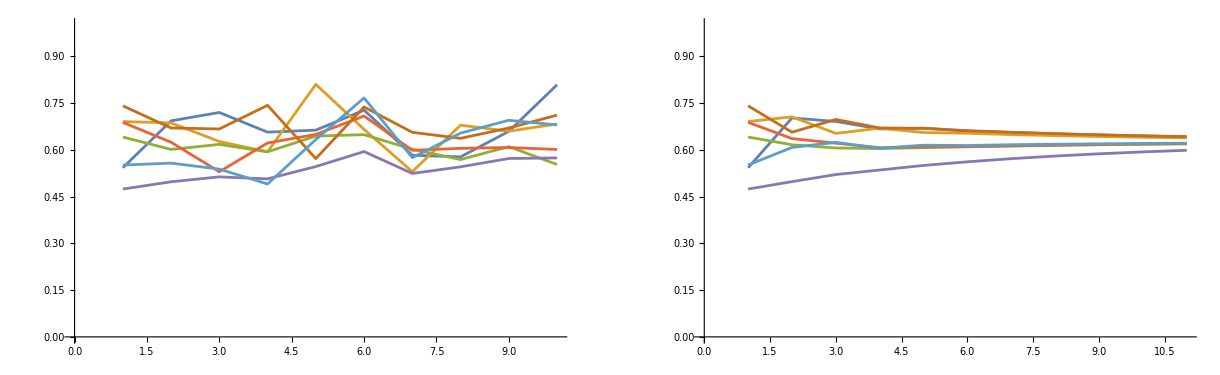

# F-J model

```mathematica
FunctionConvexity[Sum[(X[[t+1]]-DiagonalMatrix[S].W.X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).X[[1]]).(X[[t+1]]-DiagonalMatrix[S].W.X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).X[[1]]),{t,1,3}],Flatten[{W,S}]]
```

Part::partd: 部分指定 X⟦2⟧ 比对象深度更长.

Part::partd: 部分指定 X⟦1⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

FunctionConvexity[(-(-DiagonalMatrix[S]+IdentityMatrix[n]).X⟦1⟧-DiagonalMatrix[S].W.X⟦1⟧+X⟦2⟧).(-(-DiagonalMatrix[S]+IdentityMatrix[n]).X⟦1⟧-DiagonalMatrix[S].W.X⟦1⟧+X⟦2⟧)+(-(-DiagonalMatrix[S]+IdentityMatrix[n]).X⟦1⟧-DiagonalMatrix[S].W.X⟦2⟧+X⟦3⟧).(-(-DiagonalMatrix[S]+IdentityMatrix[n]).X⟦1⟧-DiagonalMatrix[S].W.X⟦2⟧+X⟦3⟧),{W,S}]

```mathematica
solveFJ = NMinimize[
   {
    Sum[(X[[t + 1]] - DiagonalMatrix[S] . W . X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).X[[1]] ) . (X[[t + 1]] - DiagonalMatrix[S] . W . X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).X[[1]] ), {t, 1,T - 1}],
    Flatten[W] ≥ ConstantArray[0, n^2],
    Flatten[W] ≤ ConstantArray[1, n^2],
    Flatten[S]≤ ConstantArray[1, n],
    Flatten[S]≥ ConstantArray[0, n],
    Total[Transpose[W]] == ConstantArray[1, n]
    } ,Flatten[{W,S}],MaxIterations -> 800,AccuracyGoal ->6];
```

```mathematica
solveFJ={0.1810907300229154,{Subscript[w, 1,1]->0.024386944548681677,Subscript[w, 1,2]->0.6762925702782425,Subscript[w, 1,3]->0.,Subscript[w, 1,4]->0.,Subscript[w, 1,5]->0.,Subscript[w, 1,6]->0.2993204851730758,Subscript[w, 1,7]->0.,Subscript[w, 2,1]->-1.470469030984134*^-7,Subscript[w, 2,2]->0.,Subscript[w, 2,3]->0.,Subscript[w, 2,4]->0.,Subscript[w, 2,5]->0.4098818531470778,Subscript[w, 2,6]->0.5901182938998254,Subscript[w, 2,7]->0.,Subscript[w, 3,1]->-7.11756276139397*^-8,Subscript[w, 3,2]->0.25059320262851903,Subscript[w, 3,3]->0.11684944244715105,Subscript[w, 3,4]->0.10904705312147545,Subscript[w, 3,5]->0.523510372978482,Subscript[w, 3,6]->0.,Subscript[w, 3,7]->0.,Subscript[w, 4,1]->-1.6925806342604766*^-7,Subscript[w, 4,2]->0.1609454003029614,Subscript[w, 4,3]->0.646573277227577,Subscript[w, 4,4]->0.,Subscript[w, 4,5]->0.19248149172752513,Subscript[w, 4,6]->0.,Subscript[w, 4,7]->0.,Subscript[w, 5,1]->-7.772852783638484*^-8,Subscript[w, 5,2]->0.26654936424495096,Subscript[w, 5,3]->0.,Subscript[w, 5,4]->0.,Subscript[w, 5,5]->0.7334507134835768,Subscript[w, 5,6]->0.,Subscript[w, 5,7]->0.,Subscript[w, 6,1]->0.17225570954338337,Subscript[w, 6,2]->0.4911360713757536,Subscript[w, 6,3]->0.2642642723359958,Subscript[w, 6,4]->0.,Subscript[w, 6,5]->0.,Subscript[w, 6,6]->0.,Subscript[w, 6,7]->0.07234394674486729,Subscript[w, 7,1]->-1.4946962356710003*^-7,Subscript[w, 7,2]->0.49872476502736357,Subscript[w, 7,3]->0.,Subscript[w, 7,4]->0.08468260316263503,Subscript[w, 7,5]->0.32057598749035954,Subscript[w, 7,6]->0.,Subscript[w, 7,7]->0.09601679378926536,Subscript[s, 1]->1.,Subscript[s, 2]->0.32206069089039135,Subscript[s, 3]->0.5270821732970324,Subscript[s, 4]->0.8540006601664517,Subscript[s, 5]->0.7149194560529604,Subscript[s, 6]->0.6789216405508893,Subscript[s, 7]->1.}}
```

{0.181091,{w_(1,1)→0.0243869,w_(1,2)→0.676293,w_(1,3)→0.,w_(1,4)→0.,w_(1,5)→0.,w_(1,6)→0.29932,w_(1,7)→0.,w_(2,1)→-1.47047×10^-7,w_(2,2)→0.,w_(2,3)→0.,w_(2,4)→0.,w_(2,5)→0.409882,w_(2,6)→0.590118,w_(2,7)→0.,w_(3,1)→-7.11756×10^-8,w_(3,2)→0.250593,w_(3,3)→0.116849,w_(3,4)→0.109047,w_(3,5)→0.52351,w_(3,6)→0.,w_(3,7)→0.,w_(4,1)→-1.69258×10^-7,w_(4,2)→0.160945,w_(4,3)→0.646573,w_(4,4)→0.,w_(4,5)→0.192481,w_(4,6)→0.,w_(4,7)→0.,w_(5,1)→-7.77285×10^-8,w_(5,2)→0.266549,w_(5,3)→0.,w_(5,4)→0.,w_(5,5)→0.733451,w_(5,6)→0.,w_(5,7)→0.,w_(6,1)→0.172256,w_(6,2)→0.491136,w_(6,3)→0.264264,w_(6,4)→0.,w_(6,5)→0.,w_(6,6)→0.,w_(6,7)→0.0723439,w_(7,1)→-1.4947×10^-7,w_(7,2)→0.498725,w_(7,3)→0.,w_(7,4)→0.0846826,w_(7,5)→0.320576,w_(7,6)→0.,w_(7,7)→0.0960168,s_1→1.,s_2→0.322061,s_3→0.527082,s_4→0.854001,s_5→0.714919,s_6→0.678922,s_7→1.}}

```mathematica
WFJMAT = Partition[Flatten[W] /. solveFJ[[2]], n]
SFJ=Flatten[S] /. solveFJ[[2]]
WFJMAT //MatrixForm
SFJ // MatrixForm
```

{{0.0243869,0.676293,0.,0.,0.,0.29932,0.},{-1.47047×10^-7,0.,0.,0.,0.409882,0.590118,0.},{-7.11756×10^-8,0.250593,0.116849,0.109047,0.52351,0.,0.},{-1.69258×10^-7,0.160945,0.646573,0.,0.192481,0.,0.},{-7.77285×10^-8,0.266549,0.,0.,0.733451,0.,0.},{0.172256,0.491136,0.264264,0.,0.,0.,0.0723439},{-1.4947×10^-7,0.498725,0.,0.0846826,0.320576,0.,0.0960168}}

{1.,0.322061,0.527082,0.854001,0.714919,0.678922,1.}

(0.0243869 | 0.676293 | 0. | 0. | 0. | 0.29932 | 0.
-1.47047×10^-7 | 0. | 0. | 0. | 0.409882 | 0.590118 | 0.
-7.11756×10^-8 | 0.250593 | 0.116849 | 0.109047 | 0.52351 | 0. | 0.
-1.69258×10^-7 | 0.160945 | 0.646573 | 0. | 0.192481 | 0. | 0.
-7.77285×10^-8 | 0.266549 | 0. | 0. | 0.733451 | 0. | 0.
0.172256 | 0.491136 | 0.264264 | 0. | 0. | 0. | 0.0723439
-1.4947×10^-7 | 0.498725 | 0. | 0.0846826 | 0.320576 | 0. | 0.0960168)

(1.
0.322061
0.527082
0.854001
0.714919
0.678922
1.)

### W=

(0.0243869 | 0.676293 | 0. | 0. | 0. | 0.29932 | 0.
-1.47047×10^-7 | 0. | 0. | 0. | 0.409882 | 0.590118 | 0.
-7.11756×10^-8 | 0.250593 | 0.116849 | 0.109047 | 0.52351 | 0. | 0.
-1.69258×10^-7 | 0.160945 | 0.646573 | 0. | 0.192481 | 0. | 0.
-7.77285×10^-8 | 0.266549 | 0. | 0. | 0.733451 | 0. | 0.
0.172256 | 0.491136 | 0.264264 | 0. | 0. | 0. | 0.0723439
-1.4947×10^-7 | 0.498725 | 0. | 0.0846826 | 0.320576 | 0. | 0.0960168)

### S=

(1.
0.322061
0.527082
0.854001
0.714919
0.678922
1.)

```mathematica
XFJ = NestList[DiagonalMatrix[SFJ].WFJMAT.# + (IdentityMatrix[n] -DiagonalMatrix[SFJ]).X[[1]]&,X[[1]], T]
```

{{0.542237,0.690464,0.640777,0.687817,0.473992,0.740787,0.551033},{0.701912,0.671452,0.604022,0.627058,0.515243,0.673524,0.607457},{0.672815,0.664114,0.607138,0.610931,0.533251,0.682035,0.611471},{0.669691,0.668109,0.610402,0.614603,0.541295,0.676942,0.612604},{0.670791,0.668203,0.613561,0.618277,0.546274,0.67855,0.617595},{0.671363,0.669166,0.615354,0.620852,0.548903,0.679522,0.620028},{0.672319,0.669697,0.616464,0.622406,0.550465,0.680351,0.621803},{0.67295,0.670061,0.617123,0.62335,0.551385,0.680926,0.622871},{0.673384,0.670292,0.61752,0.623915,0.551937,0.681292,0.62353},{0.67366,0.670434,0.61776,0.624256,0.55227,0.681523,0.623933},{0.673832,0.670522,0.617905,0.624463,0.552472,0.681666,0.624178}}

### Graph(True, FJ)

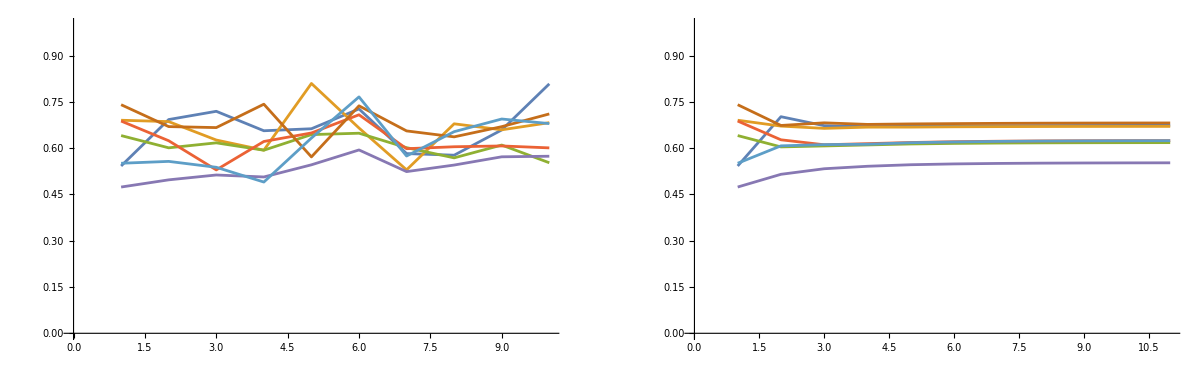

```mathematica
p1=ListLinePlot[Transpose[X],PlotRange->{0,1},ImageSize->Large];
p2=ListLinePlot[Transpose[XFJ],PlotRange->{0,1},ImageSize->Large];
GraphicsRow[{p1,p2}]
```

# F-J model with private opinions

```mathematica
Length[ConstantArray[0,n*(T-1)]]
```

63

## When XPI[[1]]=X[[1]]:

```mathematica
XPrivate=Table[Subscript[xpr, i, j], {i, 1, T}, {j, 1, n}];
XPrivate[[1]]=X[[1]];
solveFJP=NMinimize[
{
Sum[(X[[t+1]]-(DiagonalMatrix[Φ].XPrivate[[t+1]]+(IdentityMatrix[n]-DiagonalMatrix[Φ]).A.X[t])).(X[[t+1]]-(DiagonalMatrix[Φ].XPrivate[[t+1]]+(IdentityMatrix[n]-DiagonalMatrix[Φ]).A.X[t])),{t,1,T-1}],
Flatten[Table[XPrivate[[t+1]]-(DiagonalMatrix[S].(DiagonalMatrix[Diagonal[W]].XPrivate[[t]]+(W-DiagonalMatrix[Diagonal[W]]).X[[t]])+(IdentityMatrix[n]-DiagonalMatrix[S]).XPrivate[[1]]),{t,1,T-1}]]==ConstantArray[0,n*(T-1)],
Flatten[A]<=ConstantArray[1,n^2],Flatten[A]>=ConstantArray[0,n^2],Diagonal[A]==ConstantArray[0,n],
Flatten[W]>=ConstantArray[0,n^2],Flatten[W]<=ConstantArray[1,n^2],
Flatten[S]<=ConstantArray[1,n],Flatten[S]>=ConstantArray[0,n],
Flatten[Φ]<=ConstantArray[1,n],Flatten[Φ]>=ConstantArray[0,n],
Total[Transpose[A]]==ConstantArray[1,n],
Total[Transpose[W]]==ConstantArray[1,n]
},
Flatten[{W,S,Φ,A,XPrivate[[2;;T,All]]}],MaxIterations->800,AccuracyGoal->6]
```

NMinimize::nnum: 函数值 … 不是一个位于 {s_1,s_2,s_3,s_4,s_5,s_6,s_7,ϕ_1,ϕ_2,ϕ_3,«165»} = {0.791463,0.63107,0.687499,0.575455,0.297191,0.682708,0.779255,0.751474,0.662278,0.638559,«165»} 的数.

```mathematica
XPrivate=Table[Subscript[xpr, i, j], {i, 1, T}, {j, 1, n}];
XPrivate[[1]]=X[[1]]
solveFJP=NMinimize[
{
Sum[(X[[t+1]]-(DiagonalMatrix[Φ].XPrivate[[t+1]]+(IdentityMatrix[n]-DiagonalMatrix[Φ]).A.X[t])).(X[[t+1]]-(DiagonalMatrix[Φ].XPrivate[[t+1]]+(IdentityMatrix[n]-DiagonalMatrix[Φ]).A.X[t]))+(XPrivate[[t+1]]-(DiagonalMatrix[S].(DiagonalMatrix[Diagonal[W]].XPrivate[[t]]+(W-DiagonalMatrix[Diagonal[W]]).X[[t]])+(IdentityMatrix[n]-DiagonalMatrix[S]).XPrivate[[1]])).(XPrivate[[t+1]]-(DiagonalMatrix[S].(DiagonalMatrix[Diagonal[W]].XPrivate[[t]]+(W-DiagonalMatrix[Diagonal[W]]).X[[t]])+(IdentityMatrix[n]-DiagonalMatrix[S]).XPrivate[[1]])),{t,1,T-1}],
Flatten[A]<=ConstantArray[1,n^2],Flatten[A]>=ConstantArray[0,n^2],Diagonal[A]==ConstantArray[0,n],
Flatten[W]>=ConstantArray[0,n^2],Flatten[W]<=ConstantArray[1,n^2],
Flatten[S]<=ConstantArray[1,n],Flatten[S]>=ConstantArray[0,n],
Flatten[Φ]<=ConstantArray[1,n],Flatten[Φ]>=ConstantArray[0,n],
Total[Transpose[A]]==ConstantArray[1,n],
Total[Transpose[W]]==ConstantArray[1,n]
},
Flatten[{W,S,Φ,A,XPrivate[[2;;T,All]]}],MaxIterations->400,AccuracyGoal->6]
```

{0.542237,0.690464,0.640777,0.687817,0.473992,0.740787,0.551033}

NMinimize::nnum: 函数值 … 不是一个位于 {s_1,s_2,s_3,s_4,s_5,s_6,s_7,ϕ_1,ϕ_2,ϕ_3,«165»} = {0.791463,0.63107,0.687499,0.575455,0.297191,0.682708,0.779255,0.751474,0.662278,0.638559,«165»} 的数.

```mathematica
solveFJP
```

{0.098331,{w_(1,1)→0.140841,w_(1,2)→0.385122,w_(1,3)→0.,w_(1,4)→0.36792,w_(1,5)→0.,w_(1,6)→0.106117,w_(1,7)→0.,w_(2,1)→2.22279×10^-9,w_(2,2)→0.,w_(2,3)→0.,w_(2,4)→0.439669,w_(2,5)→8.74709×10^-6,w_(2,6)→0.394463,w_(2,7)→0.165859,w_(3,1)→6.60381×10^-8,w_(3,2)→8.78714×10^-10,w_(3,3)→0.690907,w_(3,4)→0.100264,w_(3,5)→0.20882,w_(3,6)→8.22057×10^-10,w_(3,7)→8.56356×10^-6,w_(4,1)→6.92023×10^-8,w_(4,2)→0.197431,w_(4,3)→0.,w_(4,4)→0.0518411,w_(4,5)→0.420512,w_(4,6)→0.330215,w_(4,7)→3.50009×10^-8,w_(5,1)→7.23224×10^-8,w_(5,2)→3.25415×10^-7,w_(5,3)→0.,w_(5,4)→0.269238,w_(5,5)→0.637503,w_(5,6)→0.,w_(5,7)→0.0932584,w_(6,1)→0.537906,w_(6,2)→0.462094,w_(6,3)→0.,w_(6,4)→0.,w_(6,5)→0.,w_(6,6)→0.,w_(6,7)→0.,w_(7,1)→4.47272×10^-9,w_(7,2)→0.0379453,w_(7,3)→0.,w_(7,4)→0.167798,w_(7,5)→0.794257,w_(7,6)→6.68232×10^-8,w_(7,7)→9.26919×10^-8,s_1→1.,s_2→1.,s_3→1.,s_4→1.,s_5→0.694789,s_6→0.775502,s_7→1.,ϕ_1→0.,ϕ_2→1.,ϕ_3→5.19168×10^-7,ϕ_4→0.,ϕ_5→0.067542,ϕ_6→0.,ϕ_7→9.40671×10^-8,a_(1,1)→0,a_(1,2)→-3.6072×10^-8,a_(1,3)→0.713471,a_(1,4)→0.286528,a_(1,5)→1.20909×10^-6,a_(1,6)→0.,a_(1,7)→1.61431×10^-8,a_(2,1)→0.00439034,a_(2,2)→0,a_(2,3)→0.0794745,a_(2,4)→0.634536,a_(2,5)→0.0490129,a_(2,6)→0.0186425,a_(2,7)→0.213943,a_(3,1)→-1.42978×10^-8,a_(3,2)→0.384498,a_(3,3)→0,a_(3,4)→2.65174×10^-8,a_(3,5)→1.00579×10^-6,a_(3,6)→0.615501,a_(3,7)→1.35033×10^-7,a_(4,1)→-7.09589×10^-9,a_(4,2)→1.28138×10^-8,a_(4,3)→2.69391×10^-8,a_(4,4)→0,a_(4,5)→1.04903×10^-7,a_(4,6)→1.,a_(4,7)→3.02492×10^-8,a_(5,1)→5.21556×10^-9,a_(5,2)→0.,a_(5,3)→0.,a_(5,4)→0.,a_(5,5)→0,a_(5,6)→0.,a_(5,7)→1.,a_(6,1)→0.999998,a_(6,2)→0.,a_(6,3)→0.,a_(6,4)→0.,a_(6,5)→7.10109×10^-7,a_(6,6)→0,a_(6,7)→8.90041×10^-7,a_(7,1)→1.,a_(7,2)→0.,a_(7,3)→0.,a_(7,4)→0.,a_(7,5)→3.66834×10^-8,a_(7,6)→0.,a_(7,7)→0,xpi_(2,1)→0.654255,xpi_(2,2)→0.685991,xpi_(2,3)→0.721438,xpi_(2,4)→0.740787,xpi_(2,5)→0.547402,xpi_(2,6)→0.542237,xpi_(2,7)→0.542237,xpi_(3,1)→0.726981,xpi_(3,2)→0.626356,xpi_(3,3)→0.59751,xpi_(3,4)→0.542237,xpi_(3,5)→0.540264,xpi_(3,6)→0.654255,xpi_(3,7)→0.654255,xpi_(4,1)→0.581672,xpi_(4,2)→0.593513,xpi_(4,3)→0.643527,xpi_(4,4)→0.654255,xpi_(4,5)→0.644283,xpi_(4,6)→0.726981,xpi_(4,7)→0.726981,xpi_(5,1)→0.646601,xpi_(5,2)→0.809609,xpi_(5,3)→0.675663,xpi_(5,4)→0.726981,xpi_(5,5)→0.714758,xpi_(5,6)→0.581672,xpi_(5,7)→0.581672,xpi_(6,1)→0.690367,xpi_(6,2)→0.665289,xpi_(6,3)→0.669313,xpi_(6,4)→0.581672,xpi_(6,5)→0.582516,xpi_(6,6)→0.646601,xpi_(6,7)→0.646601,xpi_(7,1)→0.644202,xpi_(7,2)→0.529654,xpi_(7,3)→0.653786,xpi_(7,4)→0.646601,xpi_(7,5)→0.638319,xpi_(7,6)→0.690367,xpi_(7,7)→0.690367,xpi_(8,1)→0.651727,xpi_(8,2)→0.678874,xpi_(8,3)→0.628573,xpi_(8,4)→0.690367,xpi_(8,5)→0.680564,xpi_(8,6)→0.644202,xpi_(8,7)→0.644202,xpi_(9,1)→0.646279,xpi_(9,2)→0.659458,xpi_(9,3)→0.657533,xpi_(9,4)→0.644202,xpi_(9,5)→0.639321,xpi_(9,6)→0.651727,xpi_(9,7)→0.651727,xpi_(10,1)→0.653713,xpi_(10,2)→0.682581,xpi_(10,3)→0.6547,xpi_(10,4)→0.651727,xpi_(10,5)→0.646467,xpi_(10,6)→0.646279,xpi_(10,7)→0.646279}}

```mathematica
WFJPMAT=Partition[Flatten[W]/. solveFJP[[2]],n];
SFJP=Partition[Flatten[S]/. solveFJP[[2]],n];
ΦFJP=Partition[Flatten[Φ]/. solveFJP[[2]],n];
AFJP=Partition[Flatten[A]/. solveFJP[[2]],n];
WFJPMAT//MatrixForm
SFJP//MatrixForm
ΦFJP//MatrixForm
AFJP//MatrixForm
```

(0.0244427 | 0.676263 | 0. | 0. | 0. | 0.299295 | 0.
3.13559×10^-8 | 4.60764×10^-9 | 7.63318×10^-9 | 7.81938×10^-9 | 0.410004 | 0.589996 | 0.
1.22105×10^-7 | 0.250772 | 0.115954 | 0.109299 | 0.523975 | 0. | 0.
8.87142×10^-9 | 0.160944 | 0.646567 | 1.01389×10^-8 | 0.192489 | 6.10857×10^-9 | 0.
1.28174×10^-8 | 0.26636 | 2.62793×10^-9 | 6.83173×10^-10 | 0.73364 | 2.21632×10^-9 | 0.
0.172263 | 0.491143 | 0.264257 | 0. | 0. | 0. | 0.0723379
5.08501×10^-9 | 0.498705 | 1.07561×10^-8 | 0.08467 | 0.320575 | 4.71137×10^-9 | 0.0960509)

(1. | 0.321998 | 0.526822 | 0.853994 | 0.715095 | 0.678924 | 1.)

(1. | 1. | 1. | 1. | 1. | 1. | 1.)

(0 | 0.0000129128 | 0.109095 | 0.306842 | 0.272177 | 0.0900114 | 0.221862
0.0000299579 | 0 | 0.0000180689 | 2.8678×10^-6 | 8.15706×10^-6 | 2.31759×10^-6 | 0.999939
0.00183528 | 0.000472356 | 0 | 0.00157045 | 0.960894 | 0.000904203 | 0.034324
0.46108 | 0.00952234 | 0.156844 | 0 | 0.25629 | 0.0130789 | 0.103185
0.10505 | 0.136363 | 0.177475 | 0.0932023 | 0 | 0.0189412 | 0.468968
5.94417×10^-6 | 0.673231 | 0.0595777 | 0.211306 | 0.0535989 | 0 | 0.00228024
0.928165 | 0.0000100985 | 5.34019×10^-9 | 4.65954×10^-9 | 0.0000108058 | 0.0718137 | 0)

### W=

(0.140841 | 0.385122 | 0. | 0.36792 | 0. | 0.106117 | 0.
2.22279×10^-9 | 0. | 0. | 0.439669 | 8.74709×10^-6 | 0.394463 | 0.165859
6.60381×10^-8 | 8.78714×10^-10 | 0.690907 | 0.100264 | 0.20882 | 8.22057×10^-10 | 8.56356×10^-6
6.92023×10^-8 | 0.197431 | 0. | 0.0518411 | 0.420512 | 0.330215 | 3.50009×10^-8
7.23224×10^-8 | 3.25415×10^-7 | 0. | 0.269238 | 0.637503 | 0. | 0.0932584
0.537906 | 0.462094 | 0. | 0. | 0. | 0. | 0.
4.47272×10^-9 | 0.0379453 | 0. | 0.167798 | 0.794257 | 6.68232×10^-8 | 9.26919×10^-8)

### S=

(1. | 1. | 1. | 1. | 0.694789 | 0.775502 | 1.)

### Φ=

(0. | 1. | 5.19168×10^-7 | 0. | 0.067542 | 0. | 9.40671×10^-8)

### A=

(0 | -3.6072×10^-8 | 0.713471 | 0.286528 | 1.20909×10^-6 | 0. | 1.61431×10^-8
0.00439034 | 0 | 0.0794745 | 0.634536 | 0.0490129 | 0.0186425 | 0.213943
-1.42978×10^-8 | 0.384498 | 0 | 2.65174×10^-8 | 1.00579×10^-6 | 0.615501 | 1.35033×10^-7
-7.09589×10^-9 | 1.28138×10^-8 | 2.69391×10^-8 | 0 | 1.04903×10^-7 | 1. | 3.02492×10^-8
5.21556×10^-9 | 0. | 0. | 0. | 0 | 0. | 1.
0.999998 | 0. | 0. | 0. | 7.10109×10^-7 | 0 | 8.90041×10^-7
1. | 0. | 0. | 0. | 3.66834×10^-8 | 0. | 0)

```mathematica
XPI=Table[Subscript[xpi, i, j], {i, 1, T}, {j, 1, n}]
```

{{xpi_(1,1),xpi_(1,2),xpi_(1,3),xpi_(1,4),xpi_(1,5),xpi_(1,6),xpi_(1,7)},{xpi_(2,1),xpi_(2,2),xpi_(2,3),xpi_(2,4),xpi_(2,5),xpi_(2,6),xpi_(2,7)},{xpi_(3,1),xpi_(3,2),xpi_(3,3),xpi_(3,4),xpi_(3,5),xpi_(3,6),xpi_(3,7)},{xpi_(4,1),xpi_(4,2),xpi_(4,3),xpi_(4,4),xpi_(4,5),xpi_(4,6),xpi_(4,7)},{xpi_(5,1),xpi_(5,2),xpi_(5,3),xpi_(5,4),xpi_(5,5),xpi_(5,6),xpi_(5,7)},{xpi_(6,1),xpi_(6,2),xpi_(6,3),xpi_(6,4),xpi_(6,5),xpi_(6,6),xpi_(6,7)},{xpi_(7,1),xpi_(7,2),xpi_(7,3),xpi_(7,4),xpi_(7,5),xpi_(7,6),xpi_(7,7)},{xpi_(8,1),xpi_(8,2),xpi_(8,3),xpi_(8,4),xpi_(8,5),xpi_(8,6),xpi_(8,7)},{xpi_(9,1),xpi_(9,2),xpi_(9,3),xpi_(9,4),xpi_(9,5),xpi_(9,6),xpi_(9,7)},{xpi_(10,1),xpi_(10,2),xpi_(10,3),xpi_(10,4),xpi_(10,5),xpi_(10,6),xpi_(10,7)}}

```mathematica
solveFJP
```

{0.181091,{w_(1,1)→0.0244427,w_(1,2)→0.676263,w_(1,3)→0.,w_(1,4)→0.,w_(1,5)→0.,w_(1,6)→0.299295,w_(1,7)→0.,w_(2,1)→3.13559×10^-8,w_(2,2)→4.60764×10^-9,w_(2,3)→7.63318×10^-9,w_(2,4)→7.81938×10^-9,w_(2,5)→0.410004,w_(2,6)→0.589996,w_(2,7)→0.,w_(3,1)→1.22105×10^-7,w_(3,2)→0.250772,w_(3,3)→0.115954,w_(3,4)→0.109299,w_(3,5)→0.523975,w_(3,6)→0.,w_(3,7)→0.,w_(4,1)→8.87142×10^-9,w_(4,2)→0.160944,w_(4,3)→0.646567,w_(4,4)→1.01389×10^-8,w_(4,5)→0.192489,w_(4,6)→6.10857×10^-9,w_(4,7)→0.,w_(5,1)→1.28174×10^-8,w_(5,2)→0.26636,w_(5,3)→2.62793×10^-9,w_(5,4)→6.83173×10^-10,w_(5,5)→0.73364,w_(5,6)→2.21632×10^-9,w_(5,7)→0.,w_(6,1)→0.172263,w_(6,2)→0.491143,w_(6,3)→0.264257,w_(6,4)→0.,w_(6,5)→0.,w_(6,6)→0.,w_(6,7)→0.0723379,w_(7,1)→5.08501×10^-9,w_(7,2)→0.498705,w_(7,3)→1.07561×10^-8,w_(7,4)→0.08467,w_(7,5)→0.320575,w_(7,6)→4.71137×10^-9,w_(7,7)→0.0960509,s_1→1.,s_2→0.321998,s_3→0.526822,s_4→0.853994,s_5→0.715095,s_6→0.678924,s_7→1.,ϕ_1→1.,ϕ_2→1.,ϕ_3→1.,ϕ_4→1.,ϕ_5→1.,ϕ_6→1.,ϕ_7→1.,a_(1,1)→0,a_(1,2)→0.0000129128,a_(1,3)→0.109095,a_(1,4)→0.306842,a_(1,5)→0.272177,a_(1,6)→0.0900114,a_(1,7)→0.221862,a_(2,1)→0.0000299579,a_(2,2)→0,a_(2,3)→0.0000180689,a_(2,4)→2.8678×10^-6,a_(2,5)→8.15706×10^-6,a_(2,6)→2.31759×10^-6,a_(2,7)→0.999939,a_(3,1)→0.00183528,a_(3,2)→0.000472356,a_(3,3)→0,a_(3,4)→0.00157045,a_(3,5)→0.960894,a_(3,6)→0.000904203,a_(3,7)→0.034324,a_(4,1)→0.46108,a_(4,2)→0.00952234,a_(4,3)→0.156844,a_(4,4)→0,a_(4,5)→0.25629,a_(4,6)→0.0130789,a_(4,7)→0.103185,a_(5,1)→0.10505,a_(5,2)→0.136363,a_(5,3)→0.177475,a_(5,4)→0.0932023,a_(5,5)→0,a_(5,6)→0.0189412,a_(5,7)→0.468968,a_(6,1)→5.94417×10^-6,a_(6,2)→0.673231,a_(6,3)→0.0595777,a_(6,4)→0.211306,a_(6,5)→0.0535989,a_(6,6)→0,a_(6,7)→0.00228024,a_(7,1)→0.928165,a_(7,2)→0.0000100985,a_(7,3)→5.34019×10^-9,a_(7,4)→4.65954×10^-9,a_(7,5)→0.0000108058,a_(7,6)→0.0718137,a_(7,7)→0,xpi_(2,1)→0.69269,xpi_(2,2)→0.685991,xpi_(2,3)→0.601049,xpi_(2,4)→0.623997,xpi_(2,5)→0.497273,xpi_(2,6)→0.669839,xpi_(2,7)→0.557094,xpi_(3,1)→0.719408,xpi_(3,2)→0.626356,xpi_(3,3)→0.617184,xpi_(3,4)→0.529495,xpi_(3,5)→0.513026,xpi_(3,6)→0.666616,xpi_(3,7)→0.537976,xpi_(4,1)→0.656396,xpi_(4,2)→0.593513,xpi_(4,3)→0.593332,xpi_(4,4)→0.621614,xpi_(4,5)→0.506612,xpi_(4,6)→0.742431,xpi_(4,7)→0.49017,xpi_(5,1)→0.662846,xpi_(5,2)→0.809609,xpi_(5,3)→0.643933,xpi_(5,4)→0.649233,xpi_(5,5)→0.546008,xpi_(5,6)→0.571651,xpi_(5,7)→0.632734,xpi_(6,1)→0.72706,xpi_(6,2)→0.665289,xpi_(6,3)→0.648383,xpi_(6,4)→0.708136,xpi_(6,5)→0.594167,xpi_(6,6)→0.73716,xpi_(6,7)→0.766128,xpi_(7,1)→0.582414,xpi_(7,2)→0.529654,xpi_(7,3)→0.601566,xpi_(7,4)→0.598221,xpi_(7,5)→0.523988,xpi_(7,6)→0.655859,xpi_(7,7)→0.574511,xpi_(8,1)→0.577169,xpi_(8,2)→0.678874,xpi_(8,3)→0.568535,xpi_(8,4)→0.604527,xpi_(8,5)→0.545223,xpi_(8,6)→0.636605,xpi_(8,7)→0.653399,xpi_(9,1)→0.658991,xpi_(9,2)→0.659458,xpi_(9,3)→0.610053,xpi_(9,4)→0.607142,xpi_(9,5)→0.571942,xpi_(9,6)→0.669664,xpi_(9,7)→0.694449,xpi_(10,1)→0.808328,xpi_(10,2)→0.682581,xpi_(10,3)→0.552651,xpi_(10,4)→0.600858,xpi_(10,5)→0.573838,xpi_(10,6)→0.710904,xpi_(10,7)→0.679584}}

```mathematica
XFJPP=Partition[Flatten[XPI]/. solveFJP[[2]],n]
```

{{xpi_(1,1),xpi_(1,2),xpi_(1,3),xpi_(1,4),xpi_(1,5),xpi_(1,6),xpi_(1,7)},{0.69269,0.685991,0.601049,0.623997,0.497273,0.669839,0.557094},{0.719408,0.626356,0.617184,0.529495,0.513026,0.666616,0.537976},{0.656396,0.593513,0.593332,0.621614,0.506612,0.742431,0.49017},{0.662846,0.809609,0.643933,0.649233,0.546008,0.571651,0.632734},{0.72706,0.665289,0.648383,0.708136,0.594167,0.73716,0.766128},{0.582414,0.529654,0.601566,0.598221,0.523988,0.655859,0.574511},{0.577169,0.678874,0.568535,0.604527,0.545223,0.636605,0.653399},{0.658991,0.659458,0.610053,0.607142,0.571942,0.669664,0.694449},{0.808328,0.682581,0.552651,0.600858,0.573838,0.710904,0.679584}}

```mathematica
XFJPP[[1]]=X[[1]]
```

{0.542237,0.690464,0.640777,0.687817,0.473992,0.740787,0.551033}

### min value=

0.098331

```mathematica
XFJPP=Partition[Flatten[XPI]/. solveFJP[[2]],n]
```

{{0.542237,0.690464,0.640777,0.687817,0.473992,0.740787,0.551033},{0.69269,0.685991,0.601049,0.623997,0.497273,0.669839,0.557094},{0.719408,0.626356,0.617184,0.529495,0.513026,0.666616,0.537976},{0.656396,0.593513,0.593332,0.621614,0.506612,0.742431,0.49017},{0.662846,0.809609,0.643933,0.649233,0.546008,0.571651,0.632734},{0.72706,0.665289,0.648383,0.708136,0.594167,0.73716,0.766128},{0.582414,0.529654,0.601566,0.598221,0.523988,0.655859,0.574511},{0.577169,0.678874,0.568535,0.604527,0.545223,0.636605,0.653399},{0.658991,0.659458,0.610053,0.607142,0.571942,0.669664,0.694449},{0.808328,0.682581,0.552651,0.600858,0.573838,0.710904,0.679584}}

```mathematica
XFJP=X
```

{{0.542237,0.690464,0.640777,0.687817,0.473992,0.740787,0.551033},{0.69269,0.685991,0.601049,0.623997,0.497273,0.669839,0.557094},{0.719408,0.626356,0.617184,0.529495,0.513026,0.666616,0.537976},{0.656396,0.593513,0.593332,0.621614,0.506612,0.742431,0.49017},{0.662846,0.809609,0.643933,0.649233,0.546008,0.571651,0.632734},{0.72706,0.665289,0.648383,0.708136,0.594167,0.73716,0.766128},{0.582414,0.529654,0.601566,0.598221,0.523988,0.655859,0.574511},{0.577169,0.678874,0.568535,0.604527,0.545223,0.636605,0.653399},{0.658991,0.659458,0.610053,0.607142,0.571942,0.669664,0.694449},{0.808328,0.682581,0.552651,0.600858,0.573838,0.710904,0.679584}}

```mathematica
XFJP=Table[DiagonalMatrix[Flatten[SFJP]].DiagonalMatrix[Diagonal[WFJPMAT]].XFJP[[t-1]]+DiagonalMatrix[Flatten[SFJP]].(WFJPMAT-DiagonalMatrix[Diagonal[WFJPMAT]]).XFJPP[[t]]+(IdentityMatrix[n]-DiagonalMatrix[Flatten[SFJP]]).X[[1]],{t,2,T}]
```

{{0.677643,0.661041,0.606171,0.608333,0.514372,0.682798,0.607281},{0.640027,0.662508,0.594772,0.611636,0.515227,0.667994,0.575171},{0.641161,0.676064,0.594953,0.592897,0.517235,0.643046,0.5627},{0.734645,0.648821,0.63451,0.657014,0.555031,0.731937,0.680844},{0.68674,0.686622,0.63522,0.647552,0.54821,0.698673,0.64299},{0.572251,0.661912,0.591872,0.591522,0.547641,0.618719,0.556357},{0.663865,0.661057,0.614951,0.597284,0.539245,0.665811,0.61971},{0.660501,0.670865,0.617894,0.621933,0.546688,0.678371,0.626391},{0.690481,0.67895,0.623646,0.593727,0.565109,0.692518,0.641941}}

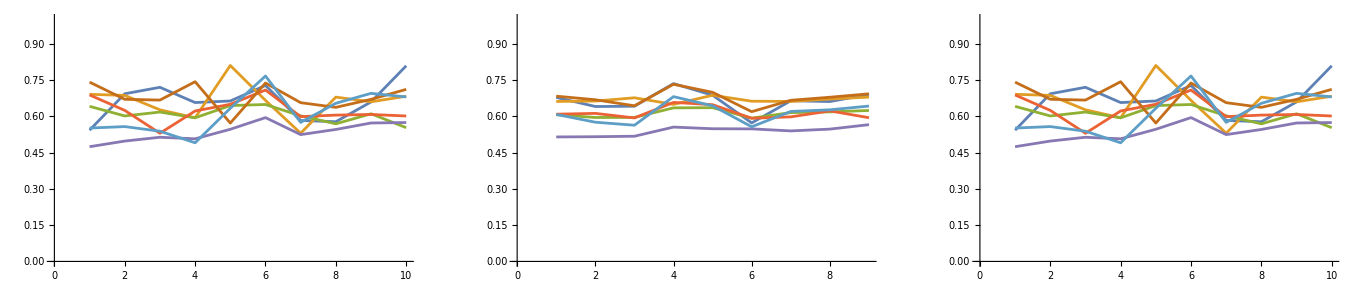

```mathematica
p1=ListLinePlot[Transpose[X],PlotRange->{0,1},ImageSize->Large];
p2=ListLinePlot[Transpose[XFJP],PlotRange->{0,1},ImageSize->Large];
p3=ListLinePlot[Transpose[XFJPP],PlotRange->{0,1},ImageSize->Large];
GraphicsRow[{p1,p2,p3}]
```

### Graph(True,expressed,private)

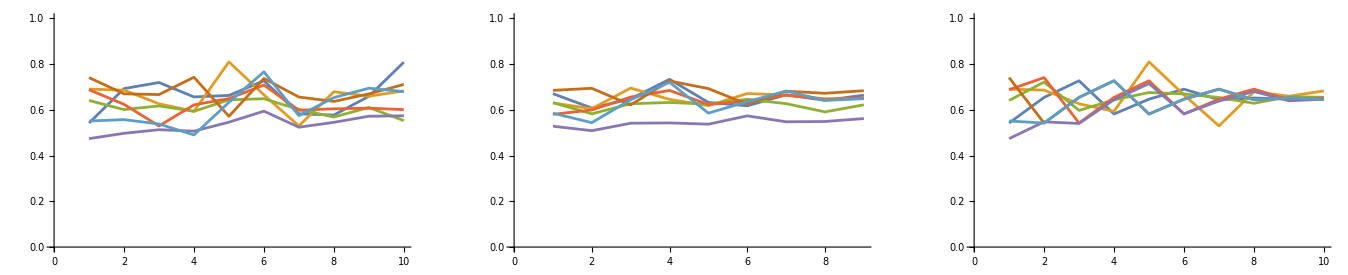

## When XPI[[1]] UNKNOW

```mathematica
XPI=Table[Subscript[xpi,i,j],{i,1,T},{j,1,n}];
```

```mathematica
XPI
```

{{xpi_(1,1),xpi_(1,2),xpi_(1,3),xpi_(1,4),xpi_(1,5),xpi_(1,6),xpi_(1,7)},{xpi_(2,1),xpi_(2,2),xpi_(2,3),xpi_(2,4),xpi_(2,5),xpi_(2,6),xpi_(2,7)},{xpi_(3,1),xpi_(3,2),xpi_(3,3),xpi_(3,4),xpi_(3,5),xpi_(3,6),xpi_(3,7)},{xpi_(4,1),xpi_(4,2),xpi_(4,3),xpi_(4,4),xpi_(4,5),xpi_(4,6),xpi_(4,7)},{xpi_(5,1),xpi_(5,2),xpi_(5,3),xpi_(5,4),xpi_(5,5),xpi_(5,6),xpi_(5,7)},{xpi_(6,1),xpi_(6,2),xpi_(6,3),xpi_(6,4),xpi_(6,5),xpi_(6,6),xpi_(6,7)},{xpi_(7,1),xpi_(7,2),xpi_(7,3),xpi_(7,4),xpi_(7,5),xpi_(7,6),xpi_(7,7)},{xpi_(8,1),xpi_(8,2),xpi_(8,3),xpi_(8,4),xpi_(8,5),xpi_(8,6),xpi_(8,7)},{xpi_(9,1),xpi_(9,2),xpi_(9,3),xpi_(9,4),xpi_(9,5),xpi_(9,6),xpi_(9,7)},{xpi_(10,1),xpi_(10,2),xpi_(10,3),xpi_(10,4),xpi_(10,5),xpi_(10,6),xpi_(10,7)}}

```mathematica
Length[ConstantArray[1,n*T]]
```

```mathematica
Flatten[XPI]<=ConstantArray[1,n*T]
```

```mathematica
Total[Transpose[W]]==ConstantArray[1,n]
```

```mathematica
solveFJPun=NMinimize[{Sum[(XPI[[t+1]]-DiagonalMatrix[S].DiagonalMatrix[Diagonal[W]].XPI[[t]]-DiagonalMatrix[S].(W-DiagonalMatrix[Diagonal[W]]).X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).XPI[[1]]).(XPI[[t+1]]-DiagonalMatrix[S].DiagonalMatrix[Diagonal[W]].XPI[[t]]-DiagonalMatrix[S].(W-DiagonalMatrix[Diagonal[W]]).X[[t]]-(IdentityMatrix[n]-DiagonalMatrix[S]).XPI[[1]]),{t,1,T-1}],Flatten[Table[X[[t]]-DiagonalMatrix[Φ].XPI[[t]]-(IdentityMatrix[n]-DiagonalMatrix[Φ]).A.X[[t-1]],{t,2,T}]]==ConstantArray[0,n*(T-1)],
Flatten[A]<=ConstantArray[1,n^2],Flatten[A]>=ConstantArray[0,n^2],Diagonal[A]==ConstantArray[0,n],
Flatten[W]>=ConstantArray[0,n^2],Flatten[W]<=ConstantArray[1,n^2],
Flatten[S]<=ConstantArray[1,n],Flatten[S]>=ConstantArray[0,n],
Flatten[Φ]<=ConstantArray[1,n],Flatten[Φ]>=ConstantArray[0,n],
Total[Transpose[A]]==ConstantArray[1,n],Total[Transpose[W]]==ConstantArray[1,n],
Flatten[XPI]<=ConstantArray[1,n*T],Flatten[XPI]>=ConstantArray[0,n*T]},
Flatten[{W,S,Φ,A,XPI}],MaxIterations->2000,AccuracyGoal->6]
```

{0.165089,{w_(1,1)→1.35254×10^-8,w_(1,2)→1.,w_(1,3)→0.,w_(1,4)→0.,w_(1,5)→0.,w_(1,6)→0.,w_(1,7)→0.,w_(2,1)→5.49018×10^-6,w_(2,2)→4.23607×10^-7,w_(2,3)→0.0000448636,w_(2,4)→0.0000163492,w_(2,5)→1.71507×10^-6,w_(2,6)→1.36494×10^-7,w_(2,7)→0.999931,w_(3,1)→0.10454,w_(3,2)→0.662543,w_(3,3)→0.,w_(3,4)→0.,w_(3,5)→0.,w_(3,6)→0.232917,w_(3,7)→0.,w_(4,1)→1.88173×10^-8,w_(4,2)→0.291963,w_(4,3)→0.693408,w_(4,4)→3.86294×10^-9,w_(4,5)→0.0146291,w_(4,6)→3.81264×10^-10,w_(4,7)→0.,w_(5,1)→9.63054×10^-9,w_(5,2)→0.279635,w_(5,3)→3.8649×10^-8,w_(5,4)→4.15826×10^-9,w_(5,5)→0.703384,w_(5,6)→0.0169812,w_(5,7)→0.,w_(6,1)→0.173017,w_(6,2)→0.493951,w_(6,3)→0.260454,w_(6,4)→0.,w_(6,5)→0.,w_(6,6)→0.,w_(6,7)→0.0725777,w_(7,1)→-5.37475×10^-9,w_(7,2)→0.331068,w_(7,3)→5.0527×10^-9,w_(7,4)→7.77444×10^-9,w_(7,5)→0.668932,w_(7,6)→0.,w_(7,7)→0.,s_1→0.486086,s_2→0.,s_3→0.334698,s_4→0.567565,s_5→0.746852,s_6→0.675697,s_7→0.890468,ϕ_1→1.,ϕ_2→1.,ϕ_3→1.,ϕ_4→1.,ϕ_5→1.,ϕ_6→1.,ϕ_7→1.,a_(1,1)→0,a_(1,2)→0.0000176196,a_(1,3)→2.25044×10^-6,a_(1,4)→0.999861,a_(1,5)→6.46045×10^-6,a_(1,6)→1.69636×10^-6,a_(1,7)→0.000111011,a_(2,1)→0.0000295476,a_(2,2)→0,a_(2,3)→1.33532×10^-7,a_(2,4)→8.34613×10^-7,a_(2,5)→4.58445×10^-6,a_(2,6)→0.0000121977,a_(2,7)→0.999953,a_(3,1)→5.41761×10^-6,a_(3,2)→7.79633×10^-6,a_(3,3)→0,a_(3,4)→0.0000115628,a_(3,5)→7.1808×10^-6,a_(3,6)→0.0000152483,a_(3,7)→0.999953,a_(4,1)→0.0000166966,a_(4,2)→0.0000158074,a_(4,3)→2.83843×10^-7,a_(4,4)→0,a_(4,5)→2.94353×10^-6,a_(4,6)→0.0000742956,a_(4,7)→0.99989,a_(5,1)→0.401982,a_(5,2)→0.0000126342,a_(5,3)→1.57225×10^-6,a_(5,4)→1.95988×10^-6,a_(5,5)→0,a_(5,6)→8.60306×10^-7,a_(5,7)→0.598001,a_(6,1)→2.09519×10^-6,a_(6,2)→5.7911×10^-6,a_(6,3)→1.02527×10^-6,a_(6,4)→0.999978,a_(6,5)→5.74607×10^-6,a_(6,6)→0,a_(6,7)→7.62395×10^-6,a_(7,1)→0.999925,a_(7,2)→0.0000297488,a_(7,3)→0.0000411043,a_(7,4)→3.13209×10^-8,a_(7,5)→2.8359×10^-8,a_(7,6)→4.31939×10^-6,a_(7,7)→0,xpi_(1,1)→0.691497,xpi_(1,2)→0.659036,xpi_(1,3)→0.574717,xpi_(1,4)→0.60256,xpi_(1,5)→0.454771,xpi_(1,6)→0.739433,xpi_(1,7)→1.,xpi_(2,1)→0.69269,xpi_(2,2)→0.685991,xpi_(2,3)→0.601049,xpi_(2,4)→0.623997,xpi_(2,5)→0.497273,xpi_(2,6)→0.669839,xpi_(2,7)→0.557094,xpi_(3,1)→0.719408,xpi_(3,2)→0.626356,xpi_(3,3)→0.617184,xpi_(3,4)→0.529495,xpi_(3,5)→0.513026,xpi_(3,6)→0.666616,xpi_(3,7)→0.537976,xpi_(4,1)→0.656396,xpi_(4,2)→0.593513,xpi_(4,3)→0.593332,xpi_(4,4)→0.621614,xpi_(4,5)→0.506612,xpi_(4,6)→0.742431,xpi_(4,7)→0.49017,xpi_(5,1)→0.662846,xpi_(5,2)→0.809609,xpi_(5,3)→0.643933,xpi_(5,4)→0.649233,xpi_(5,5)→0.546008,xpi_(5,6)→0.571651,xpi_(5,7)→0.632734,xpi_(6,1)→0.72706,xpi_(6,2)→0.665289,xpi_(6,3)→0.648383,xpi_(6,4)→0.708136,xpi_(6,5)→0.594167,xpi_(6,6)→0.73716,xpi_(6,7)→0.766128,xpi_(7,1)→0.582414,xpi_(7,2)→0.529654,xpi_(7,3)→0.601566,xpi_(7,4)→0.598221,xpi_(7,5)→0.523988,xpi_(7,6)→0.655859,xpi_(7,7)→0.574511,xpi_(8,1)→0.577169,xpi_(8,2)→0.678874,xpi_(8,3)→0.568535,xpi_(8,4)→0.604527,xpi_(8,5)→0.545223,xpi_(8,6)→0.636605,xpi_(8,7)→0.653399,xpi_(9,1)→0.658991,xpi_(9,2)→0.659458,xpi_(9,3)→0.610053,xpi_(9,4)→0.607142,xpi_(9,5)→0.571942,xpi_(9,6)→0.669664,xpi_(9,7)→0.694449,xpi_(10,1)→0.808328,xpi_(10,2)→0.682581,xpi_(10,3)→0.552651,xpi_(10,4)→0.600858,xpi_(10,5)→0.573838,xpi_(10,6)→0.710904,xpi_(10,7)→0.679584}}

```mathematica
solveFJPun
```

{0.0437586,{w_(1,1)→0.30081,w_(1,2)→0.287905,w_(1,3)→0.0078072,w_(1,4)→1.88599×10^-10,w_(1,5)→0.152286,w_(1,6)→0.251192,w_(1,7)→1.53033×10^-10,w_(2,1)→0.262198,w_(2,2)→1.50404×10^-9,w_(2,3)→0.0979947,w_(2,4)→0.259036,w_(2,5)→7.92769×10^-10,w_(2,6)→0.380771,w_(2,7)→2.9636×10^-10,w_(3,1)→0.000608362,w_(3,2)→1.14516×10^-10,w_(3,3)→0.813809,w_(3,4)→0.106442,w_(3,5)→0.00765078,w_(3,6)→0.0714901,w_(3,7)→1.55356×10^-10,w_(4,1)→9.97267×10^-10,w_(4,2)→0.320285,w_(4,3)→0.178857,w_(4,4)→0.371199,w_(4,5)→0.0993104,w_(4,6)→0.0303476,w_(4,7)→1.83045×10^-10,w_(5,1)→1.92193×10^-9,w_(5,2)→0.139616,w_(5,3)→0.0835488,w_(5,4)→0.388589,w_(5,5)→0.189385,w_(5,6)→0.0738904,w_(5,7)→0.12497,w_(6,1)→0.0547635,w_(6,2)→0.450506,w_(6,3)→3.32565×10^-10,w_(6,4)→2.29864×10^-10,w_(6,5)→0.406856,w_(6,6)→0.0135058,w_(6,7)→0.0743684,w_(7,1)→4.30744×10^-10,w_(7,2)→0.149659,w_(7,3)→1.88698×10^-10,w_(7,4)→0.457926,w_(7,5)→7.07531×10^-6,w_(7,6)→0.150303,w_(7,7)→0.242104,s_1→1.,s_2→0.960833,s_3→1.,s_4→1.,s_5→0.507603,s_6→0.74545,s_7→1.,ϕ_1→2.47376×10^-10,ϕ_2→7.2427×10^-10,ϕ_3→7.20624×10^-10,ϕ_4→1.02437×10^-9,ϕ_5→3.69073×10^-10,ϕ_6→4.19262×10^-10,ϕ_7→0.0868885,a_(1,1)→0,a_(1,2)→2.27665×10^-10,a_(1,3)→2.90178×10^-10,a_(1,4)→2.68675×10^-10,a_(1,5)→0.699932,a_(1,6)→1.967×10^-10,a_(1,7)→0.300068,a_(2,1)→0.00258358,a_(2,2)→0,a_(2,3)→0.630688,a_(2,4)→7.10343×10^-10,a_(2,5)→3.18337×10^-10,a_(2,6)→0.366729,a_(2,7)→4.76375×10^-10,a_(3,1)→0.283712,a_(3,2)→4.55844×10^-10,a_(3,3)→0,a_(3,4)→1.05926×10^-9,a_(3,5)→0.716288,a_(3,6)→1.55589×10^-10,a_(3,7)→1.03242×10^-9,a_(4,1)→0.168614,a_(4,2)→5.82495×10^-10,a_(4,3)→0.573341,a_(4,4)→0,a_(4,5)→4.48499×10^-10,a_(4,6)→1.82628×10^-9,a_(4,7)→0.258044,a_(5,1)→1.32394×10^-10,a_(5,2)→4.07032×10^-10,a_(5,3)→1.34975×10^-10,a_(5,4)→4.47996×10^-10,a_(5,5)→0,a_(5,6)→0.308049,a_(5,7)→0.691951,a_(6,1)→1.,a_(6,2)→2.77972×10^-10,a_(6,3)→6.51796×10^-10,a_(6,4)→3.35639×10^-10,a_(6,5)→4.03748×10^-10,a_(6,6)→0,a_(6,7)→3.40734×10^-10,a_(7,1)→5.78577×10^-10,a_(7,2)→0.834025,a_(7,3)→2.65639×10^-10,a_(7,4)→0.165975,a_(7,5)→1.51103×10^-10,a_(7,6)→5.48652×10^-10,a_(7,7)→0,xpi_(1,1)→1.,xpi_(1,2)→1.,xpi_(1,3)→0.0573423,xpi_(1,4)→0.298756,xpi_(1,5)→0.132765,xpi_(1,6)→0.889383,xpi_(1,7)→0.904589,xpi_(2,1)→0.364367,xpi_(2,2)→0.364909,xpi_(2,3)→0.378808,xpi_(2,4)→0.434904,xpi_(2,5)→0.899884,xpi_(2,6)→1.,xpi_(2,7)→0.855234,xpi_(3,1)→0.886487,xpi_(3,2)→0.606585,xpi_(3,3)→0.747951,xpi_(3,4)→0.499305,xpi_(3,5)→0.89982,xpi_(3,6)→0.364367,xpi_(3,7)→0.390579,xpi_(4,1)→0.747009,xpi_(4,2)→0.607636,xpi_(4,3)→0.896037,xpi_(4,4)→0.679113,xpi_(4,5)→0.382521,xpi_(4,6)→0.886487,xpi_(4,7)→0.580221,xpi_(5,1)→0.441846,xpi_(5,2)→0.892147,xpi_(5,3)→0.485935,xpi_(5,4)→0.789415,xpi_(5,5)→0.674571,xpi_(5,6)→0.747009,xpi_(5,7)→0.620638,xpi_(6,1)→0.658388,xpi_(6,2)→0.581568,xpi_(6,3)→0.608541,xpi_(6,4)→0.513251,xpi_(6,5)→0.659564,xpi_(6,6)→0.441846,xpi_(6,7)→0.865618,xpi_(7,1)→0.721396,xpi_(7,2)→0.547538,xpi_(7,3)→0.65923,xpi_(7,4)→0.683276,xpi_(7,5)→0.735063,xpi_(7,6)→0.658388,xpi_(7,7)→0.570607,xpi_(8,1)→0.685713,xpi_(8,2)→0.659083,xpi_(8,3)→0.731183,xpi_(8,4)→0.64685,xpi_(8,5)→0.597652,xpi_(8,6)→0.721396,xpi_(8,7)→0.577315,xpi_(9,1)→0.591549,xpi_(9,2)→0.727474,xpi_(9,3)→0.62264,xpi_(9,4)→0.68382,xpi_(9,5)→0.621705,xpi_(9,6)→0.685713,xpi_(9,7)→0.660301,xpi_(10,1)→0.633287,xpi_(10,2)→0.645691,xpi_(10,3)→0.613149,xpi_(10,4)→0.627113,xpi_(10,5)→0.668134,xpi_(10,6)→0.591549,xpi_(10,7)→0.71669}}

```mathematica
WFJPMAT=Partition[Flatten[W]/. solveFJPun[[2]],n];
SFJP=Partition[Flatten[S]/. solveFJPun[[2]],n];
ΦFJP=Partition[Flatten[Φ]/. solveFJPun[[2]],n];
AFJP=Partition[Flatten[A]/. solveFJPun[[2]],n]
minvalue=solveFJPun[[1]]
WFJPMAT//MatrixForm
SFJP//MatrixForm
ΦFJP//MatrixForm
AFJP//MatrixForm
```

{{0,0.0000176196,2.25044×10^-6,0.999861,6.46045×10^-6,1.69636×10^-6,0.000111011},{0.0000295476,0,1.33532×10^-7,8.34613×10^-7,4.58445×10^-6,0.0000121977,0.999953},{5.41761×10^-6,7.79633×10^-6,0,0.0000115628,7.1808×10^-6,0.0000152483,0.999953},{0.0000166966,0.0000158074,2.83843×10^-7,0,2.94353×10^-6,0.0000742956,0.99989},{0.401982,0.0000126342,1.57225×10^-6,1.95988×10^-6,0,8.60306×10^-7,0.598001},{2.09519×10^-6,5.7911×10^-6,1.02527×10^-6,0.999978,5.74607×10^-6,0,7.62395×10^-6},{0.999925,0.0000297488,0.0000411043,3.13209×10^-8,2.8359×10^-8,4.31939×10^-6,0}}

0.165089

(1.35254×10^-8 | 1. | 0. | 0. | 0. | 0. | 0.
5.49018×10^-6 | 4.23607×10^-7 | 0.0000448636 | 0.0000163492 | 1.71507×10^-6 | 1.36494×10^-7 | 0.999931
0.10454 | 0.662543 | 0. | 0. | 0. | 0.232917 | 0.
1.88173×10^-8 | 0.291963 | 0.693408 | 3.86294×10^-9 | 0.0146291 | 3.81264×10^-10 | 0.
9.63054×10^-9 | 0.279635 | 3.8649×10^-8 | 4.15826×10^-9 | 0.703384 | 0.0169812 | 0.
0.173017 | 0.493951 | 0.260454 | 0. | 0. | 0. | 0.0725777
-5.37475×10^-9 | 0.331068 | 5.0527×10^-9 | 7.77444×10^-9 | 0.668932 | 0. | 0.)

(0.486086 | 0. | 0.334698 | 0.567565 | 0.746852 | 0.675697 | 0.890468)

(1. | 1. | 1. | 1. | 1. | 1. | 1.)

(0 | 0.0000176196 | 2.25044×10^-6 | 0.999861 | 6.46045×10^-6 | 1.69636×10^-6 | 0.000111011
0.0000295476 | 0 | 1.33532×10^-7 | 8.34613×10^-7 | 4.58445×10^-6 | 0.0000121977 | 0.999953
5.41761×10^-6 | 7.79633×10^-6 | 0 | 0.0000115628 | 7.1808×10^-6 | 0.0000152483 | 0.999953
0.0000166966 | 0.0000158074 | 2.83843×10^-7 | 0 | 2.94353×10^-6 | 0.0000742956 | 0.99989
0.401982 | 0.0000126342 | 1.57225×10^-6 | 1.95988×10^-6 | 0 | 8.60306×10^-7 | 0.598001
2.09519×10^-6 | 5.7911×10^-6 | 1.02527×10^-6 | 0.999978 | 5.74607×10^-6 | 0 | 7.62395×10^-6
0.999925 | 0.0000297488 | 0.0000411043 | 3.13209×10^-8 | 2.8359×10^-8 | 4.31939×10^-6 | 0)

### W=

(0.30081 | 0.287905 | 0.0078072 | 1.88599×10^-10 | 0.152286 | 0.251192 | 1.53033×10^-10
0.262198 | 1.50404×10^-9 | 0.0979947 | 0.259036 | 7.92769×10^-10 | 0.380771 | 2.9636×10^-10
0.000608362 | 1.14516×10^-10 | 0.813809 | 0.106442 | 0.00765078 | 0.0714901 | 1.55356×10^-10
9.97267×10^-10 | 0.320285 | 0.178857 | 0.371199 | 0.0993104 | 0.0303476 | 1.83045×10^-10
1.92193×10^-9 | 0.139616 | 0.0835488 | 0.388589 | 0.189385 | 0.0738904 | 0.12497
0.0547635 | 0.450506 | 3.32565×10^-10 | 2.29864×10^-10 | 0.406856 | 0.0135058 | 0.0743684
4.30744×10^-10 | 0.149659 | 1.88698×10^-10 | 0.457926 | 7.07531×10^-6 | 0.150303 | 0.242104)

### S=

(1. | 0.960833 | 1. | 1. | 0.507603 | 0.74545 | 1.)

### Φ=

(2.47376×10^-10 | 7.2427×10^-10 | 7.20624×10^-10 | 1.02437×10^-9 | 3.69073×10^-10 | 4.19262×10^-10 | 0.0868885)

### A=

(0 | 2.27665×10^-10 | 2.90178×10^-10 | 2.68675×10^-10 | 0.699932 | 1.967×10^-10 | 0.300068
0.00258358 | 0 | 0.630688 | 7.10343×10^-10 | 3.18337×10^-10 | 0.366729 | 4.76375×10^-10
0.283712 | 4.55844×10^-10 | 0 | 1.05926×10^-9 | 0.716288 | 1.55589×10^-10 | 1.03242×10^-9
0.168614 | 5.82495×10^-10 | 0.573341 | 0 | 4.48499×10^-10 | 1.82628×10^-9 | 0.258044
1.32394×10^-10 | 4.07032×10^-10 | 1.34975×10^-10 | 4.47996×10^-10 | 0 | 0.308049 | 0.691951
1. | 2.77972×10^-10 | 6.51796×10^-10 | 3.35639×10^-10 | 4.03748×10^-10 | 0 | 3.40734×10^-10
5.78577×10^-10 | 0.834025 | 2.65639×10^-10 | 0.165975 | 1.51103×10^-10 | 5.48652×10^-10 | 0)

### min value=

0.0437586

```mathematica
XFJPP=Partition[Flatten[XPI]/. solveFJPun[[2]],n]
```

{{0.691497,0.659036,0.574717,0.60256,0.454771,0.739433,1.},{0.69269,0.685991,0.601049,0.623997,0.497273,0.669839,0.557094},{0.719408,0.626356,0.617184,0.529495,0.513026,0.666616,0.537976},{0.656396,0.593513,0.593332,0.621614,0.506612,0.742431,0.49017},{0.662846,0.809609,0.643933,0.649233,0.546008,0.571651,0.632734},{0.72706,0.665289,0.648383,0.708136,0.594167,0.73716,0.766128},{0.582414,0.529654,0.601566,0.598221,0.523988,0.655859,0.574511},{0.577169,0.678874,0.568535,0.604527,0.545223,0.636605,0.653399},{0.658991,0.659458,0.610053,0.607142,0.571942,0.669664,0.694449},{0.808328,0.682581,0.552651,0.600858,0.573838,0.710904,0.679584}}

```mathematica
XFJP=X
```

{{0.542237,0.690464,0.640777,0.687817,0.473992,0.740787,0.551033},{0.69269,0.685991,0.601049,0.623997,0.497273,0.669839,0.557094},{0.719408,0.626356,0.617184,0.529495,0.513026,0.666616,0.537976},{0.656396,0.593513,0.593332,0.621614,0.506612,0.742431,0.49017},{0.662846,0.809609,0.643933,0.649233,0.546008,0.571651,0.632734},{0.72706,0.665289,0.648383,0.708136,0.594167,0.73716,0.766128},{0.582414,0.529654,0.601566,0.598221,0.523988,0.655859,0.574511},{0.577169,0.678874,0.568535,0.604527,0.545223,0.636605,0.653399},{0.658991,0.659458,0.610053,0.607142,0.571942,0.669664,0.694449},{0.808328,0.682581,0.552651,0.600858,0.573838,0.710904,0.679584}}

```mathematica
XFJP=Table[DiagonalMatrix[Flatten[SFJP]].DiagonalMatrix[Diagonal[WFJPMAT]].XFJP[[t-1]]+DiagonalMatrix[Flatten[SFJP]].(WFJPMAT-DiagonalMatrix[Diagonal[WFJPMAT]]).XFJPP[[t]]+(IdentityMatrix[n]-DiagonalMatrix[Flatten[SFJP]]).X[[1]],{t,2,T}]
```

{{0.612113,0.690464,0.654885,0.651784,0.520751,0.683275,0.558797},{0.583126,0.690464,0.642345,0.648383,0.520486,0.668396,0.550599},{0.567162,0.690464,0.638767,0.633501,0.522863,0.643526,0.537096},{0.672203,0.690464,0.673599,0.689551,0.562459,0.732301,0.624269},{0.602051,0.690464,0.656745,0.667787,0.555113,0.698965,0.61041},{0.53612,0.690464,0.615269,0.626303,0.551054,0.619149,0.52862},{0.608654,0.690464,0.646674,0.638207,0.545107,0.666395,0.58526},{0.599216,0.690464,0.647809,0.651551,0.552627,0.6788,0.595452},{0.610456,0.690464,0.661376,0.632808,0.572015,0.693145,0.603398}}

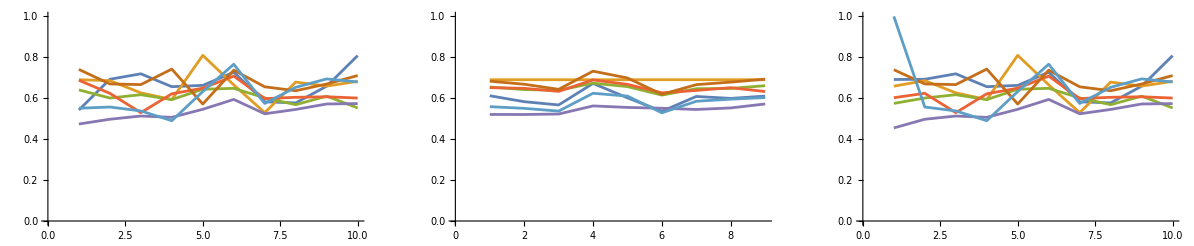

```mathematica
p1=ListLinePlot[Transpose[X],PlotRange->{0,1},ImageSize->Large];
p2=ListLinePlot[Transpose[XFJP],PlotRange->{0,1},ImageSize->Large];
p3=ListLinePlot[Transpose[XFJPP],PlotRange->{0,1},ImageSize->Large];
GraphicsRow[{p1,p2,p3}]
```

### Graph(True,expressed,private)